## LLM Scalability and Spin-Glass Transition

### Sequence Accuracy Rate

#### Motivation

Accuracy rate is among the most fundamental and widely adopted evaluation metrics in machine learning, especially for classification and other discriminative tasks. Its appeal lies in the clarity of its definition: each input has a well-defined ground-truth label, and the model’s prediction can be judged unambiguously as correct or incorrect. This binary criterion makes accuracy a natural measure of performance, enabling direct comparison across models and datasets.

However, this paradigm does not directly extend to large language models (LLMs). Many LLM applications—such as machine translation, summarization, or dialogue—are inherently sequence-to-sequence generation problems. In these settings, the model generates text probabilistically, token by token, sampling from a distribution of plausible continuations. Crucially, there is rarely a single “correct” output: multiple valid translations, summaries, or conversational responses may exist. Consequently, simple exact-match accuracy is insufficient for evaluation, and researchers rely instead on a suite of task-specific metrics (e.g., BLEU, ROUGE, perplexity, or human judgment) that capture fluency, coherence, and relevance.

Yet this limitation is context-dependent. In scientific domains—including mathematics, physics, and computer science—the nature of the task often changes. Here, many problems admit a unique correct solution: a definite numerical value, a closed-form expression, or a precise code output. For instance, the question “what is 2342342 + 3442342” has only one acceptable answer, and the model’s response must exactly match the correct sequence of digits to be considered correct. In such applications, the probabilistic flexibility of LLMs does not diminish the importance of exact correctness. The evaluation once again reduces to a binary criterion: either the model outputs the correct sequence or it does not.

This observation motivates the introduction of a new evaluation concept tailored for LLMs in scientific applications: the Sequence Accuracy Rate (SAR). SAR measures the proportion of problem instances for which the LLM produces the exact correct sequence as output. By aligning the evaluation of LLMs with the well-established standard of accuracy in classification, SAR provides a rigorous and interpretable metric for assessing LLMs in domains where precision and correctness are paramount.

#### Definition

Let 𝒟={(x_(k),y_(k))}_(k=1)^K be a dataset consists of pairs of sequences, where each input sequence x_(k) is deterministically mapped to a unique correct output sequence y_(k). An LLM trained on the dataset defines a conditional probability distribution p_θ(y|x) over output sequences.

Definition: The Sequence Accuracy Rate (SAR) is defined as the geometric mean of the model’s probability on correct sequences:

SAR(p_θ;𝒟)=exp(1/K∑_(k=1)^K log p_θ(y_(k)|x_(k))).

Remarks:

SAR∈(0,1]; it equals to 1 iff ∀k:p_θ(y_(k)|x_(k))=1.

SAR can serve as a learning objective. Maximizing SAR is equivalent to minimizing the sequence-level cross entropy.

(Optional length normalization) If sequence y_(k) are all of the same length N,

SAR^(1/N)=PPL^-1,

links SAR to token-level perplexity (PPL).

#### Observation

In our experiments, we observed that the Sequence Accuracy Rate (SAR) exhibits a strong dependence on the output sequence length N. A naive expectation might suggest an exponential decay: since the probability of reproducing every token correctly diminishes multiplicatively with length, one would anticipate SAR∼ⅇ^(-α N) for some rate α. However, our empirical results deviate significantly from this simple picture. Instead of a smooth exponential decay, SAR displays a distinct crossover behavior: it remains relatively high for short sequences, then undergoes a rapid drop at a characteristic length scale N_crs, with the transition extending over a range N_rng.

This nontrivial scaling suggests that sequence-level accuracy in LLMs is not governed solely by independent token-level errors, but is shaped by more complex mechanisms, such as correlations in generation, context-length effects, or model calibration at different sequence scales. The presence of a well-defined crossover length motivates us to investigate the underlying principles that control when and how LLMs transition from reliable to unreliable sequence generation, particularly in the scientific problem-solving regime where exact correctness is essential.

### Sherrington-Kirkpatrick (SK) model

#### Model Setting

To gain insight into the observed crossover behavior of SAR, we propose a simplified toy model. Consider an output sequence y=(y_1,y_2,…,y_N) of length N. For each token y_i, we assign an Ising variable s_i=±1, where

s_i=Piecewise[{{+1, y_i is correct,}, {-1, otherwise.}}]

An all-correct out-put sequence corresponds to s_i=+1 for all i=1,…,N, which will be denote as s=1 jointly.

If each token were generated independently with a token-level accuracy rate p_tok, the expected sequence accuracy would scale as

SAR=p_tok^N,

which decays exponentially with sequence length N. The underlying energy model for the Ising variable is simply

E[s]=-h∑_i s_i,

such that

SAR:=ⅇ^(-E[s=1])/(∑_[s] ⅇ^(-E[s]))=(1/(1+ⅇ^(-2h)))^N,

meaning that the external field h parametrize the token-level accuracy rate as

p_tok=1/(1+ⅇ^(-2h)).

However, this prediction Eq. (DisplayFormulaNumbered) fails capture the crossover behavior observed in experiments.

#### Model Hamiltonian

We hypothesize that the deviation arises from all-to-all correlations among tokens during sequence generation. The self-attention mechanism in LLMs inherently couples every token to every other token, introducing dependencies beyond the independent-token picture. These correlations are not purely constructive: noise, interference, or internal competition within the network can generate effective random coupling strengths J_ij between the Ising variables s_i (the token correctness label). Such couplings modify the collective statistics of sequence correctness, producing a non-exponential decay and the observed crossover in SAR.

We propose the following energy model

E_J[s]=-∑_(i<j) J_ij s_i s_j-h∑_i s_i.

s_i=±1 for i=1,2,…,N are N Ising variables, representing the correctness of the ith token y_i in the output sequence generated by the LLM.

The coupling strengths J_ij are drawn independently from Gaussian distribution with zero mean and finite variance:

𝔼_J J_ij=0, 𝔼_J J_ij^2=J_0^2.

They model the noisy all-to-all correlation in token generation, and J_0 characters the noise strength, which is assumed to be weak.

h is the external magnetic field, parameterizing the token-level accuracy rate via Eq. (DisplayFormulaNumbered). A strong external field h corresponds to a high token-level accuracy, which is typically assumed.

This model is also known as the Sherrington-Kirkpatrick (SK) model in spin-glass physics.

For a particular random realization of J_ij, the probability to observe the Ising sequence s is

p_J[s]=1/Z_J ⅇ^(-E_J[s]),

where Z_J is the partition function

Z_J=∑_[s] ⅇ^(-E_J[s]).

Specifically, SAR is associated with p_J[s=1] under geometric mean over random realizations of the coupling J,

SAR:=exp(𝔼_J log p_J[s=1]).

#### Phase Diagram (Numerics)

To investigate the sequence accuracy phenomenon, we performed numerical simulations of the SK model externally in PyTorch. Here are the SAR data.

```mathematica
SetDirectory[NotebookDirectory[]];
ds=Block[{results,data,keys},
results=Import["sk_quartiles_results.json"];
data=Association["data"/.results];
keys=DeleteCases[Keys@data,x_/;StringMatchQ[x,__~~"completed"]];
Dataset[AssociationThread[{"n","J0","h","low","mid","high"}->Join[First@StringCases[#,"n"~~n__~~"_j0"~~j0__~~"_h"~~h0__:>ToExpression/@{n,j0,h0}],"quartiles"/.data[#]]]&/@keys]]
```

Dataset[<>]

Data collected at the following grid points in the J_0-h parameter space.

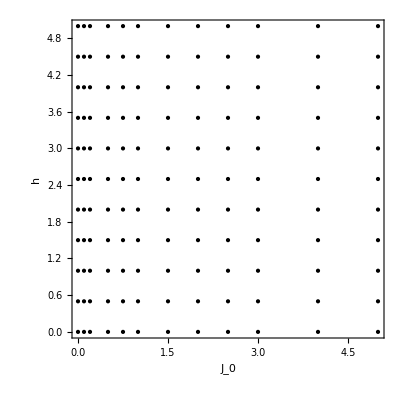

```mathematica
Graphics[Point[Normal[ds[Select[#n==1&],{"J0","h"}][[Values]]]],Frame->True,FrameLabel->{"\!\(J\_0\)","\!\(h\)"}]
```

At fixed h, how SAR p_0 depends on J_0 and N. It shows that the crossover size scales with J_0 as N_crs~J_0^-1.

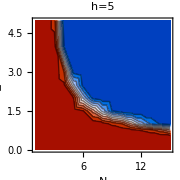
-Graphics--Graphics-

```mathematica
Block[{h=5},Row[{ListContourPlot[Normal[ds[Select[#h==5&],{"n","J0","mid"}][[Values]]],FrameLabel->{"\!\(N\)","\!\(J\_0\)"},PlotLabel->StringTemplate["\!\(h=`1`\)"][h],PlotRange->All,ImageSize->180],Graphics[Raster[List/@Range[0,1,0.02],{{0,0},{1,1}},ColorFunction->"BlueRedSplit"],Frame->True,FrameTicks->{{None,All},{None,None}},AspectRatio->10,PlotLabel->Style["\!\(p\_0\)",Black,"Text"],ImageSize->{Automatic,120}]}]]
```

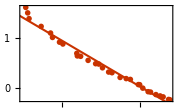
-Graphics-
2.77469-1.14232 x

```mathematica
Block[{data,lm},data=First@Cases[ListContourPlot[Normal[ds[Select[#h==5&],{"n","J0","mid"}][[Values]]],Contours->{0.5},ContourShading->None,PlotRange->All],GraphicsComplex[pts_,prm_]:>pts[[First@Cases[prm,Line[idx_]:>idx,∞]]],∞];
lm=LinearModelFit[Log[data],x,x];
Column[{Show[ListPlot[Log[data]],Plot[lm[x],{x,0,5}],Frame->True,ImageSize->180],lm["BestFit"]}]]
```

At given (J_0,h) point, the SAR decays with N as

```mathematica
Block[{J0=1,h=3,dat,mdl},
dat=Join[{{0,1}},Normal[ds[Select[#J0==J0&&#h==h&],{"n","mid"}][[Values]]]];
mdl=NonlinearModelFit[dat,LogisticSigmoid[-Exp[a] x+Exp[b]],{{a,0},{b,1}},x];
Show[Plot[mdl[x],{x,0,15},PlotStyle->Directive[Gray,Dashed]],Graphics[Translate[{Point[{0,0}],{AbsoluteThickness[1.2],Line[{0,#}&/@{#4-#3,#2-#3}],Translate[Line[Offset/@{{-2,0},{2,0}}],{0,#}]&/@{#4-#3,#2-#3}}},{#1,#3}]&@@@Normal[ds[Select[#J0==J0&&#h==h&],{"n","low","mid","high"}][[Values]]],Frame->True,AspectRatio->0.6],FrameLabel->{"\!\(N\)","\!\(p\_0\)"},PlotLabel->StringTemplate["\!\(J\_0=`1`,h=`2`\)"][J0,h],ImageSize->200]]
```

-Graphics-

Consider fitting with Fermi-Dirac function

p_0=1/(ⅇ^((N-N_crs)/+N_rng)+1).

```mathematica
ps=Dataset[Block[{dat,mdl,J0,h},
J0=#["J0"];h=#["h"];
dat=Join[{{0,1}},Normal[ds[Select[#J0==J0&&#h==h&],{"n","mid"}][[Values]]]];
mdl=NonlinearModelFit[dat,LogisticSigmoid[-Exp[-logδn] (n-Exp[logn0])],{{logδn,0},{logn0,1}},n];
Merge[{#,KeyMap[ToString,Association[mdl["BestFitParameters"]]]},First]
]&/@Normal[ds[Select[#n==1&],{"J0","h"}]]]
```

Center: Crossover system size.

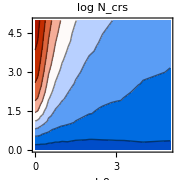

```mathematica
ListContourPlot[Normal[ps[All,{"J0","h","logn0"}][[Values]]],Contours->Range[0,5,0.5],PlotRange->All,FrameLabel->{"\!\(J\_0\)","\!\(h\)"},PlotLabel->"\!\(log N\_crs\)",ImageSize->180]
```

Width: Range of the crossover region.

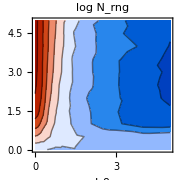

```mathematica
ListContourPlot[Normal[ps[All,{"J0","h","logδn"}][[Values]]],PlotRange->All,FrameLabel->{"\!\(J\_0\)","\!\(h\)"},PlotLabel->"\!\(log N\_rng\)",ImageSize->180]
```

##### Backup

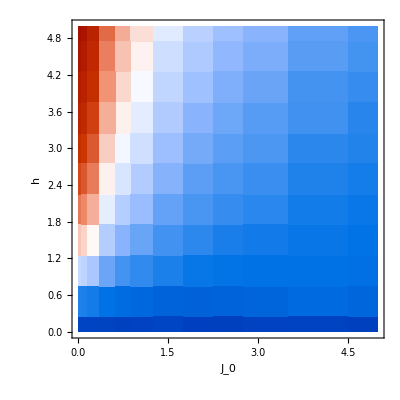

```mathematica
ListDensityPlot[Normal[ps[All,{"J0","h","logn0"}][[Values]]],PlotRange->All,InterpolationOrder->0,FrameLabel->{"\!\(J\_0\)","\!\(h\)"}]
```

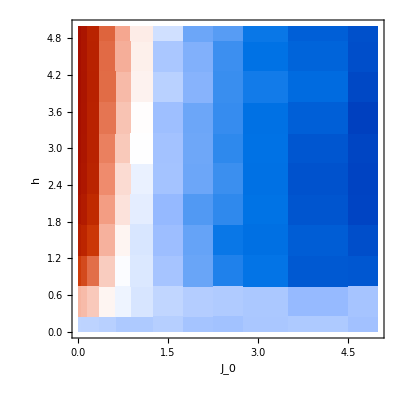

```mathematica
ListDensityPlot[Normal[ps[All,{"J0","h","logδn"}][[Values]]],PlotRange->All,InterpolationOrder->0,FrameLabel->{"\!\(J\_0\)","\!\(h\)"}]
```

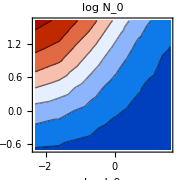

```mathematica
ListContourPlot[Normal[ps[All,{"J0","h","logn0"}][All,{"J0"->Log,"h"->Log}][[Values]]],PlotRange->All,FrameLabel->{"\!\(log J\_0\)","\!\(log h\)"},PlotLabel->"\!\(log N\_0\)",ImageSize->180]
```

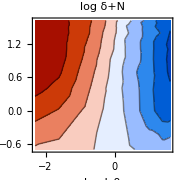

```mathematica
ListContourPlot[Normal[ps[All,{"J0","h","logδn"}][All,{"J0"->Log,"h"->Log}][[Values]]],PlotRange->All,FrameLabel->{"\!\(log J\_0\)","\!\(log h\)"},PlotLabel->"\!\(log δ+N\)",ImageSize->180]
```

#### Replica Theory

From Eq. (DisplayFormulaNumbered), it is straight forward to show that

log SAR=h N-𝔼_J log Z_J.

Show Eq. (DisplayFormulaNumbered).

Given Eq. (DisplayFormulaNumbered),

E_J[s=1]=-∑_(i<j) J_ij-h∑_i 1
=-∑_(i<j) J_ij-h N.

Therefore, by definition Eq. (DisplayFormulaNumbered),

log SAR=𝔼_J log p_J[s=1]
=𝔼_J log(1/Z_J ⅇ^(-E_J[s]))
=𝔼_J (log ⅇ^(-E_J[s])-log Z_J)
=𝔼_J (-E_J[s]- log Z_J)
=𝔼_J (∑_(i<j) J_ij+h N-log Z_J).

Using the setting 𝔼_J J_ij=0 in Eq. (DisplayFormulaNumbered),

log SAR=𝔼_J (h N-log Z_J)
=h N-𝔼_J log Z_J.

However, the expectation 𝔼_J log Z_J in Eq. (DisplayFormulaNumbered) is intractable. Instead, physicists introduce the “replica trick,” based on the mathematical identity:

𝔼_J log Z_J=lim_(n->0) ∂_n (𝔼_J Z_J^n).

where by definition

𝔼_J Z_J^n=(𝔼_J(∑_[σ] exp( ∑_(i<j) J_ij s_i s_j+h ∑_i s_i)))^n.

This involves calculating the partition function for n identical copies (or “replicas”) of the system,

Z_J^n=∑_[s] exp(-∑_(a=1)^n E_J[s^a])
=∑_[s] exp(∑_(a=1)^n ∑_(i<j) J_ij s_i^a s_j^a+h∑_(a=1)^n ∑_i s_i^a),

where we have extended the Ising variables from s_i to s_i^a with i=1,…,N and a=1,…,n.

N - number of sites (sequence length),

n - number of replica.

Averaging Z_J^n over the random coupling J,

𝔼_J Z_J^n=Ω^n∑_[s] exp(J_0^2∑_(i<j,a<b) s_i^a s_j^a s_i^b s_j^b+h∑_(i,a) s_i^a),
with Ω=exp(J_0^2/4 N(N-1)).

Derive Eq. (DisplayFormulaNumbered).

According to Eq. (DisplayFormulaNumbered),

Z_J^n=∑_[s] exp(∑_(a=1)^n ∑_(i<j) J_ij s_i^a s_j^a+h∑_(a=1)^n ∑_i s_i^a)
=∑_[s] ∏_(i<j) exp(∑_(a=1)^n J_ij s_i^a s_j^a)exp(h∑_(a=1)^n ∑_i s_i^a).

Because J_ij are independent Gaussian random variables, the average 𝔼_J Z_J^n boils down to averaging each factor independently

𝔼_J Z_J^n=∑_[s] ∏_(i<j) (𝔼_J exp(∑_(a=1)^n J_ij s_i^a s_j^a))exp(h∑_(a=1)^n ∑_i s_i^a).

First focus on the term for a single pair (i,j), denote C_ij=∑_(a=1)^n s_i^a s_j^a to simplify the notation,

𝔼_J exp(∑_(a=1)^n J_ij s_i^a s_j^a)=𝔼_J exp(J_ij C_ij)
=1/(√(2π)J_0)∫ⅆ J_ijexp(J_ij C_ij)exp(-J_ij^2/(2 J_0^2))
=1/(√(2π)J_0)∫ⅆ J_ijexp(-J_ij^2/(2 J_0^2)+J_ij C_ij)
=exp(J_0^2/2 C_ij^2)
=exp(J_0^2/2(∑_(a=1)^n s_i^a s_j^a)^2).

Therefore, the average partition function is

𝔼_J Z_J^n=∑_[s] ∏_(i<j) exp(J_0^2/2(∑_(a=1)^n s_i^a s_j^a)^2)exp(h∑_(a=1)^n ∑_i s_i^a)
=∑_[s] exp(J_0^2/2∑_(i<j) (∑_(a=1)^n s_i^a s_j^a)^2+h∑_(a=1)^n ∑_i s_i^a).

The summation in the J_0^2 term can be further expanded as

∑_(i<j) (∑_(a=1)^n s_i^a s_j^a)^2=∑_(i<j) (∑_(a=1)^n (s_i^a s_j^a)^2+2∑_(a<b) s_i^a s_j^a s_i^b s_j^b)
=∑_(i<j) (∑_(a=1)^n 1+2∑_(a<b) s_i^a s_j^a s_i^b s_j^b)
=∑_(i<j) n+2∑_(i<j) ∑_(a<b) s_i^a s_j^a s_i^b s_j^b
=(n N (N-1))/2+2∑_(i<j) ∑_(a<b) s_i^a s_j^a s_i^b s_j^b.

Define Ω=exp(J_0^2 N(N-1)/4) to absorb the constant factor, we have

𝔼_J Z_J^n=∑_[s] exp( J_0^2/4 n N (N-1)+J_0^2∑_(i<j) ∑_(a<b) s_i^a s_j^a s_i^b s_j^b+h∑_(a=1)^n ∑_i s_i^a)
=Ω^n∑_[s] exp( J_0^2∑_(i<j) ∑_(a<b) s_i^a s_j^a s_i^b s_j^b+h∑_(a=1)^n ∑_i s_i^a).

This produces a plaquette Ising model defined on the K_N×K_n product graph (where K_N or K_n denotes the complete graph of N or n vertices). The model has a self-duality under N↔n.

Example: K_4×K_3 graph

```mathematica
GraphProduct[CompleteGraph[4],CompleteGraph[3],GraphLayout->"SpringElectricalEmbedding",VertexStyle->Black,EdgeShapeFunction->Function[{pts,e},{Switch[PossibleZeroQ[e[[1]]-e[[2]]],{True,False},Red,{False,True},Blue,_,Purple],Line[pts]}],ImageSize->100]
```

-Graphics-

#### Small-J_0 Expansion

If we assume the noise strength J_0 is weak, we can proceed with small-J_0 expansion:

𝔼_J Z_J^n=Ω^n∑_[s] ⅇ^(h∑_(i,a) s_i^a)(1+J_0^2∑_(i<j,a<b) s_i^a s_j^a s_i^b s_j^b+J_0^4/2(∑_(i<j,a<b) s_i^a s_j^a s_i^b s_j^b)^2+…).

Now the Boltzmann weight can be factor to each spin,

ⅇ^(h∑_(i,a) s_i^a)=∏_(i,a) ⅇ^(h s_i^a),

the spin configuration summation can be carried out independently, and the calculation is tractable. For each spin,

the partition function:

z:=∑_s ⅇ^(h s)=2 cosh h,

the magnetization:

m:=⟨s⟩=1/z∑_s s ⅇ^(h s)=tanh h.

Therefore,

𝔼_J Z_J^n=Ω^n z^(n N)(1+J_0^2/4 N (N-1) n (n-1) m^4+J_0^4/2 N (N-1) n (n-1) (1/4+1/2(N+n-4)m^4+(N-2)(n-2) m^6+1/4(1/4 N (N-1) n (n-1)-(2N-3)(2n-3))m^8)+…).

Derive Eq. (DisplayFormulaNumbered).

J_0^2 term

⟨∑_(i<j,a<b) s_i^a s_j^a s_i^b s_j^b⟩=∑_(i<j,a<b) ⟨s_i^a s_j^a s_i^b s_j^b⟩
=(N (N-1))/(2!)×(n (n-1))/(2!) m^4
=1/4 N (N-1) n (n-1) m^4.

Explain: ∑_(i<j,a<b)  counts the number of plaquettes on K_N×K_n, which amounts to choosing one edge from K_N and one edge of K_n independently. Each summand represents a plaquette single-covered by the four-spin interaction.

```mathematica
HighlightGraph[GraphProduct[CompleteGraph[4],CompleteGraph[3],GraphLayout->"SpringElectricalEmbedding",VertexStyle->Black,EdgeShapeFunction->Function[{pts,e},{Switch[PossibleZeroQ[e[[1]]-e[[2]]],{True,False},Red,{False,True},Blue,_,Purple],Line[pts]}]],{{1,1}<->{1,2},{1,2}<->{2,2},{2,2}<->{2,1},{2,1}<->{1,1}},GraphHighlightStyle->"Thick",ImageSize->100]
```

-Graphics-

J_0^4 terms

⟨(∑_(i<j,a<b) s_i^a s_j^a s_i^b s_j^b)^2⟩
=(A)+(B)+(B')+(C)+(D)

(A) term

(A)=∑_(i<j
a<b) ⟨(s_i^a s_j^a s_i^b s_j^b)^2⟩
=(N (N-1))/(2!)×(n (n-1))/(2!)
=1/4 N (N-1) n (n-1)

Explain: This term counts the plaquettes double-covered by the four-spin interaction.

(B) term

(B)=2∑_(i<j<k
a<b) (⟨s_i^a s_j^a s_i^b s_j^b s_i^a s_k^a s_i^b s_k^b⟩+⟨s_i^a s_j^a s_i^b s_j^b s_j^a s_k^a s_j^b s_k^b⟩+⟨s_i^a s_k^a s_i^b s_k^b s_j^a s_k^a s_j^b s_k^b⟩)
=2∑_(i<j<k
a<b) (⟨s_j^a s_j^b s_k^a s_k^b⟩+⟨s_i^a s_i^b s_k^a s_k^b⟩+⟨s_i^a s_i^b s_j^a s_j^b⟩)
=2×(N (N-1)(N-2))/(3!)×(n (n-1))/(2!)×3 m^4
=1/2 N (N-1)(N-2)n (n-1) m^4.

Explain: This term counts all the edge-sharing plaquette pairs on the graph, where the shared edge is an K_n edge.

```mathematica
HighlightGraph[GraphProduct[CompleteGraph[4],CompleteGraph[3],GraphLayout->"SpringElectricalEmbedding",VertexStyle->Black,EdgeShapeFunction->Function[{pts,e},{Switch[PossibleZeroQ[e[[1]]-e[[2]]],{True,False},Red,{False,True},Blue,_,Purple],Line[pts]}]],{{1,1}<->{1,2},{1,2}<->{2,2},{2,2}<->{2,1},{2,1}<->{1,1},{1,1}<->{3,1},{3,1}<->{3,2},{3,2}<->{1,2}},GraphHighlightStyle->"Thick",ImageSize->100]
```

-Graphics-

(B') term (the N↔n dual of (B) term)

(B')=1/2 N (N-1)n (n-1) (n-2) m^4.

Explain: This term counts all the edge-sharing plaquette pairs on the graph, where the shared edge is an K_N edge.

(C) term

(C)=2∑_(i<j<k
a<b<c) (((⟨s_i^a s_j^a s_i^b s_j^b s_i^a s_k^a s_i^c s_k^c⟩+(i,j,k) cyclic)+(a,b,c) cyclic)+((⟨s_i^a s_j^a s_i^c s_j^c s_i^a s_k^a s_i^b s_k^b⟩+(i,j,k) cyclic)+(a,b,c) cyclic))
=2∑_(i<j<k
a<b<c) (((⟨s_j^a s_i^b s_j^b s_k^a s_i^c s_k^c⟩+(i,j,k) cyclic)+(a,b,c) cyclic)+((⟨s_j^a s_i^c s_j^c s_k^a s_i^b s_k^b⟩+(i,j,k) cyclic)+(a,b,c) cyclic))
=2×(N (N-1) (N-2))/(3!)×(n (n-1) (n-2))/(3!)×3×3×2 m^6
=N (N-1) (N-2)n (n-1) (n-2) m^6.

Explain: This term counts all the single-corner-sharing plaquette pairs on the graph.

```mathematica
HighlightGraph[GraphProduct[CompleteGraph[4],CompleteGraph[3],GraphLayout->"SpringElectricalEmbedding",VertexStyle->Black,EdgeShapeFunction->Function[{pts,e},{Switch[PossibleZeroQ[e[[1]]-e[[2]]],{True,False},Red,{False,True},Blue,_,Purple],Line[pts]}]],{{1,1}<->{1,2},{1,2}<->{2,2},{2,2}<->{2,1},{2,1}<->{1,1},{2,2}<->{3,2},{3,2}<->{3,3},{3,3}<->{2,3},{2,3}<->{2,2}},GraphHighlightStyle->"Thick",ImageSize->100]
```

-Graphics-

(D) term

(D)=2∑_((i<j)≠(k<l)
(a<b)≠(c<d)) ⟨s_i^a s_j^a s_i^b s_j^b s_k^c s_l^c s_k^d s_l^d⟩
=(((N (N-1))/(2!)×(n (n-1))/(2!))^2-1/4 N (N-1) n (n-1) -1/2 N (N-1)(N-2)n (n-1) ×2-N (N-1) (N-2)n (n-1) (n-2)) m^8
=1/4 N (N-1) n (n-1)(1/4 N (N-1) n (n-1)-(2N-3)(2n-3))m^8.

Explain: This term collects all the remaining non-intersecting plaquette pairs on the graph.

```mathematica
HighlightGraph[GraphProduct[CompleteGraph[4],CompleteGraph[3],GraphLayout->"SpringElectricalEmbedding",VertexStyle->Black,EdgeShapeFunction->Function[{pts,e},{Switch[PossibleZeroQ[e[[1]]-e[[2]]],{True,False},Red,{False,True},Blue,_,Purple],Line[pts]}]],{{1,1}<->{1,2},{1,2}<->{2,2},{2,2}<->{2,1},{2,1}<->{1,1},{3,2}<->{4,2},{4,2}<->{4,3},{4,3}<->{3,3},{3,3}<->{3,2}},GraphHighlightStyle->"Thick",ImageSize->100]
```

-Graphics-

Direct counting is non-trivial. However, we can use the fact that all plaquette pairs (regardless of intersection pattern) on the graph must add up to ((N (N-1))/(2!)×(n (n-1))/(2!))^2, subtracting from this total number by the number of all different types of intersecting plaquette pairs that had been counted in terms (A), (B), (B'), (C), the remaining number must be the coefficient of (D).

Putting all terms together, Eq. (DisplayFormulaNumbered) reads

⟨(∑_(i<j,a<b) s_i^a s_j^a s_i^b s_j^b)^2⟩=1/4 N (N-1) n (n-1) +1/2(N (N-1)(N-2)n (n-1)+N (N-1)n (n-1) (n-2))m^4+N (N-1) (N-2)n (n-1) (n-2) m^6+1/4 N (N-1) n (n-1)(1/4 N (N-1) n (n-1)-(2N-3)(2n-3))m^8
=N (N-1) n (n-1) (1/4+1/2(N+n-4)m^4+(N-2)(n-2) m^6+1/4(1/4 N (N-1) n (n-1)-(2N-3)(2n-3))m^8).

In conclusion,

𝔼_J Z_J^n=(Ω^n(2 cosh h))^(n N)(1+J_0^2⟨∑_(i<j,a<b) s_i^a s_j^a s_i^b s_j^b⟩+J_0^4/2⟨(∑_(i<j,a<b) s_i^a s_j^a s_i^b s_j^b)^2⟩+…)
=(Ω^n(2 cosh h))^(n N)(1+J_0^2/4 N (N-1) n (n-1) m^4+J_0^4/2 N (N-1) n (n-1) (1/4+1/2(N+n-4)m^4+(N-2)(n-2) m^6+1/4(1/4 N (N-1) n (n-1)-(2N-3)(2n-3))m^8)+…).

Verification of Eq. (DisplayFormulaNumbered) for explicit (N,n) values.

```mathematica
Block[{Ν=4,n=5,series1,series2},
series1=Expand[Normal[Series[Exp[J0^2 Sum[s[i,a]s[j,a]s[i,b]s[j,b],{i,2,Ν},{j,1,i-1},{a,2,n},{b,1,a-1}]],{J0,0,4}]]]/.s[__]^2:>1/._s->m;
series2=Expand[1+J0^2{Ν(Ν-1)n(n-1)/4}.{m^4}+J0^4/2 Ν(Ν-1)n(n-1){1/4,(Ν+n-4)/2,(Ν-2)(n-2),(Ν(Ν-1)n(n-1)/4-(2Ν-3)(2n-3))/4}.{1,m^4,m^6,m^8}];
Column@{series1,series2}]
```

1+30 J0^4+60 J0^2 m^4+300 J0^4 m^4+720 J0^4 m^6+750 J0^4 m^8
1+30 J0^4+60 J0^2 m^4+300 J0^4 m^4+720 J0^4 m^6+750 J0^4 m^8

Now we can take the replica limit as required in Eq. (DisplayFormulaNumbered),

𝔼_J log Z_J=lim_(n->0) ∂_n (𝔼_J Z_J^n)
=log Ω+N log z-J_0^2/4 N (N-1)m^4-J_0^4/2 N(N-1)(1/4+1/2(N-4)m^4-2(N-2)m^6+3/4(2N-3)m^8)+…

Compute the replica limit Eq. (DisplayFormulaNumbered).

```mathematica
SeriesCoefficient[Ω^n z^(n Ν)(1+J0^2{Ν(Ν-1)n(n-1)/4}.{m^4}+J0^4/2 Ν(Ν-1)n(n-1){1/4,(Ν+n-4)/2,(Ν-2)(n-2),(Ν(Ν-1)n(n-1)/4-(2Ν-3)(2n-3))/4}.{1,m^4,m^6,m^8}),{n,0,1}]
```

-1/4 J0^2 m^4 (-1+Ν) Ν+1/2 J0^4 (-1+Ν) Ν (-1/4-1/2 m^4 (-4+Ν)+2 m^6 (-2+Ν)-3/4 m^8 (-3+2 Ν))+Ν Log[z]+Log[Ω]

Finally, we are interested in the SAR. Substitute Eq. (DisplayFormulaNumbered) in Eq. (DisplayFormulaNumbered), we arrive at the result

log SAR=N (h-log(2 cosh h))+J_0^2/4 N(N-1)(-1+(tanh h)^4+J_0^2(1/2+(N-4)(tanh h)^4-4(N-2)(tanh h)^6+3/2(2N-3)(tanh h)^8))+𝒪(J_0^6)

Derive Eq. (DisplayFormulaNumbered).

log SAR=h N-𝔼_J log Z_J
=h N-log Ω-N log z+J_0^2/4 N (N-1)m^4+J_0^4/2 N(N-1)(1/4+1/2(N-4)m^4-2(N-2)m^6+3/4(2N-3)m^8)+𝒪(J_0^6)
=h N-J_0^2/4 N(N-1)-N log(2 cosh h)+J_0^2/4 N (N-1)(tanh h)^4+J_0^4/2 N(N-1)(1/4+1/2(N-4)(tanh h)^4-2(N-2)(tanh h)^6+3/4(2N-3)(tanh h)^8)+𝒪(J_0^6)
=N (h-log(2 cosh h))+J_0^2/4 N(N-1)(-1+(tanh h)^4+J_0^2(1/2+(N-4)(tanh h)^4-4(N-2)(tanh h)^6+3/2(2N-3)(tanh h)^8))+𝒪(J_0^6)

Compare with numerics:

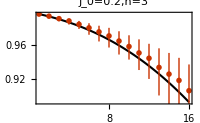

```mathematica
Block[{h=3,J0=0.2,logSAR},
logSAR[Ν_]:=Ν(h-Log[2 Cosh[h]])+J0^2/4Ν(Ν-1)(-1+Tanh[h]^4+J0^2(1/2+(Ν-4)Tanh[h]^4-4(Ν-2) Tanh[h]^6+3/2(2Ν-3)Tanh[h]^8));
Show[Plot[Exp[logSAR[Ν]],{Ν,1,16},PlotStyle->Black,PlotLabel->StringTemplate["\!\(J\_0=`1`,h=`2`\)"][J0,h],FrameLabel->{"System size \!\(N\)","\!\(SAR\)"},ImageSize->200],
Block[{Νmax=16,M=1000},
ListPlot[Table[{Ν,Block[{cf},cf=N@Append[Times@@@Subsets[#,{2}],Total[#]]&/@Tuples[{-1,1},Ν];
Around[#2,{#1-#2,#3-#2}]&@@Exp[Quartiles[Log[Last@#/Total@#]]]&@Exp[cf.Append[J0 RandomVariate[NormalDistribution[0,1],{Ν(Ν-1)/2,M}],ConstantArray[h,M]]]]},{Ν,1,Νmax}]]]]]
```

Small-J_0 and large-h limit.

log SAR=-ⅇ^(-2h) N (1+2J_0^2(N-1)+2(J_0^4(N-1))^2).

Derive Eq. (DisplayFormulaNumbered) by large-h expansion.

```mathematica
Normal@Series[Block[{h=Log[eh],logSAR},
logSAR=Ν(h-Log[2 Cosh[h]])+J0^2/4Ν(Ν-1)(-1+Tanh[h]^4+J0^2(1/2+(Ν-4)Tanh[h]^4-4(Ν-2) Tanh[h]^6+3/2(2Ν-3)Tanh[h]^8))],{eh,∞,4}]/.eh->Exp[h]
```

ⅇ^(-2 h) (-Ν+1/4 J0^2 (-8-8 J0^2 (-1+Ν)) (-1+Ν) Ν)+ⅇ^(-4 h) (Ν/2+1/4 J0^2 (32+128 J0^2 (-1+Ν)) (-1+Ν) Ν)

For large h, the difference between Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) is negligible.

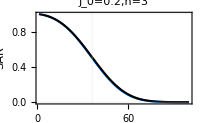

```mathematica
Block[{h=3,J0=0.2,logSAR,logSAR2},
logSAR[Ν_]:=Ν(h-Log[2 Cosh[h]])+J0^2/4Ν(Ν-1)(-1+Tanh[h]^4+J0^2(1/2+(Ν-4)Tanh[h]^4-4(Ν-2) Tanh[h]^6+3/2(2Ν-3)Tanh[h]^8));
logSAR2[Ν_]:=-Exp[-2h]Ν(1+2J0^2 (Ν-1)+2J0^4 (Ν-1)^2);
Plot[{Exp[logSAR2[Ν]],Exp[logSAR[Ν]]},{Ν,1,100},GridLines->{{Root[-Exp[2h] Log[2]+(1-2 J0^2+2 J0^4) #1+(2 J0^2-4 J0^4) #1^2+2 J0^4 #1^3&,1]},{0,1}},PlotRange->All,PlotStyle->{Blue,Black},PlotLabel->StringTemplate["\!\(J\_0=`1`,h=`2`\)"][J0,h],FrameLabel->{"System size \!\(N\)","\!\(SAR\)"},ImageSize->200]]
```

Crossover scale N_crs.

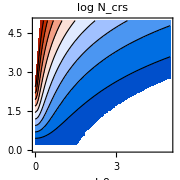

```mathematica
ContourPlot[Log[Root[-Exp[2h] Log[2]+(1-2 J0^2+2 J0^4) #1+(2 J0^2-4 J0^4) #1^2+2 J0^4 #1^3&,1]],{J0,0,5},{h,0,5},Contours->Range[0,5,0.5],PlotRange->{0,5},FrameLabel->{"\!\(J\_0\)","\!\(h\)"},PlotLabel->"\!\(log N\_crs\)",ImageSize->180]
```

This does not look like the numerics, because the perturbative expansion result is only valid for small J_0.

#### Empirical Formula for SAR

Motivated by Eq. (DisplayFormulaNumbered), we propose an empirical formula for SAR

SAR(N)=exp(-N exp((2 J_0^2)/(1+2 J_0)(N-1)-2h)),

which seems to work reasonably well for a wide range of J_0 with relatively large h.

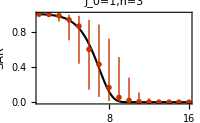

```mathematica
Block[{h=3,J0=1,logSAR},
logSAR[Ν_]:=-Ν Exp[2J0^2 (Ν-1)/(1+2J0)-2h];
Show[Plot[Exp[logSAR[Ν]],{Ν,1,16},PlotRange->All,PlotStyle->Black,PlotLabel->StringTemplate["\!\(J\_0=`1`,h=`2`\)"][J0,h],FrameLabel->{"System size \!\(N\)","\!\(SAR\)"},ImageSize->200],
Block[{Νmax=16,M=1000},
ListPlot[Table[{Ν,Block[{cf},cf=N@Append[Times@@@Subsets[#,{2}],Total[#]]&/@Tuples[{-1,1},Ν];
Around[#2,{#1-#2,#3-#2}]&@@Exp[Quartiles[Log[Last@#/Total@#]]]&@Exp[cf.Append[J0 RandomVariate[NormalDistribution[0,1],{Ν(Ν-1)/2,M}],ConstantArray[h,M]]]]},{Ν,1,Νmax}]]]]]
```

Define the crossover scale N_crs by the solution of SAR(N_crs)=1/2, Eq. (DisplayFormulaNumbered) shows

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

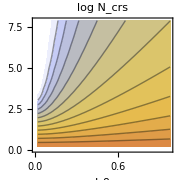

```mathematica
Block[{Νcrs},
Νcrs[J0_?NumericQ,h_?NumericQ]:=Ν/.FindRoot[-Ν Exp[2J0^2 (Ν-1)/(1+2J0)-2h]==Log[1/2],{Ν,h(1+2J0)/(2J0^2)}];
ListContourPlot[Flatten[Table[{J0,h,Log[Νcrs[J0,h]]},{J0,0.02,1,0.04},{h,0.1,8,0.2}],1],Contours->Range[0,6,0.5],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],ColorFunction->"BeachColors",PlotRange->{0,6},FrameLabel->{"\!\(J\_0\)","\!\(h\)"},PlotLabel->"\!\(log N\_crs\)",ImageSize->180]]
```

This is similar to what we observed in the numerics.

import torch

#### Fitting result for letter replacement task

We propose an empirical formula for SAR

SAR(N)=exp(-N exp((2 J_0^2)/(1+2 J_0)(N-1)-2h)),

Define the crossover scale N_crs by the solution of SAR(N_crs)=1/2, then fit the data with formula below

SAR(N)=exp(-N β_0 α^(N-1)), α=exp((2 J_0^2)/(1+2 J_0)), β_0=exp(-2h)

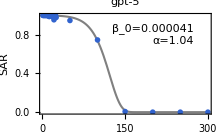
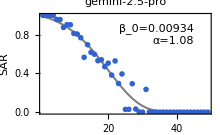
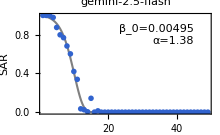
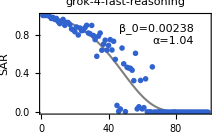
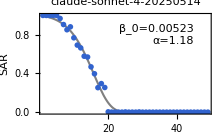

```mathematica
Block[{file,series,models,g1,g2,g3,g4,g5},file=FileNameJoin[{NotebookDirectory[],"letter_replace_13","records","letter_replace_13_plot.pt"}];
series=GetPy["import torch, numpy as np\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"{k: np.stack([v['L'], v['accuracy']], axis=1).tolist() for k, v in d['series'].items()}"];
models=Association@Table[key->NonlinearModelFit[series[key],Exp[-Ν Exp[α (Ν-1)-β]],{{α,<|"gpt-5"->0.02,"gemini-2.5-flash"->0.1,"gemini-2.5-pro"->0.1,"grok-4-fast-reasoning"->0.1,"claude-sonnet-4-20250514"->0.1|>[key]},{β,<|"gpt-5"->8,"gemini-2.5-flash"->6,"gemini-2.5-pro"->6,"grok-4-fast-reasoning"->6,"claude-sonnet-4-20250514"->6|>[key]}},Ν],{key,Keys@series}];
{g1,g2,g3,g4,g5}=Table[Show[Plot[models[key][Ν],{Ν,series[key]⟦1,1⟧,series[key]⟦-1,1⟧},PlotStyle->Gray],ListPlot[series[key]],PlotLabel->key,PlotRange->All,Epilog->Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@{Exp[-β],Exp[α]}/.models[key]["BestFitParameters"]),LineSpacing->{0,12}],Scaled@{0.9,0.9},{1,1}],ImageSize->220,FrameLabel->{"String length \!\(N\)","SAR"}],{key,Keys@series}];
Column[{Row@{g1,g2,g3},Row@{g4,g5}},Alignment->Center]]
```

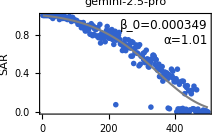
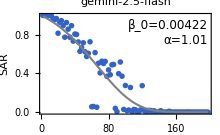
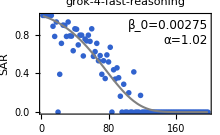
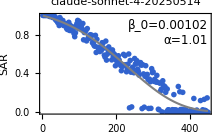

```mathematica
Block[{file,series,models,g1,g2,g3,g4},file=FileNameJoin[{NotebookDirectory[],"plus","records","plus_plot.pt"}];
series=GetPy["import torch, numpy as np\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"{k: np.stack([v['L'], v['accuracy']], axis=1).tolist() for k, v in d['series'].items()}"];
models=Association@Table[key->NonlinearModelFit[series[key],Exp[-Ν Exp[α (Ν-1)-β]],{{α,<|"gpt-5"->0.02,"gemini-2.5-flash"->0.01,"gemini-2.5-pro"->0.001,"grok-4-fast-reasoning"->0.1,"claude-sonnet-4-20250514"->0.01|>[key]},{β,<|"gpt-5"->8,"gemini-2.5-flash"->6,"gemini-2.5-pro"->6,"grok-4-fast-reasoning"->6,"claude-sonnet-4-20250514"->6|>[key]}},Ν],{key,Keys@series}];
{g1,g2,g3,g4}=Table[Show[ListPlot[series[key]],Plot[models[key][Ν],{Ν,series[key][[1,1]],series[key][[-1,1]]},PlotStyle->Gray],PlotLabel->key,PlotRange->All,Epilog->Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@{Exp[-β],Exp[α]}/. models[key]["BestFitParameters"]),12,LineSpacing->{0,12}],Scaled@{0.98,0.95},{1,1}],ImageSize->220,FrameLabel->{"Digit length \!\(N\)","SAR"}],{key,Keys@series}];
Column[{Row@{g1,g2},Row@{g3,g4}},Alignment->Center]]
```

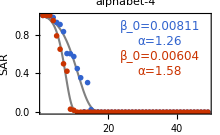
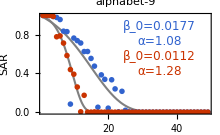
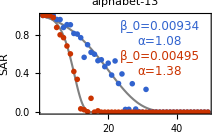
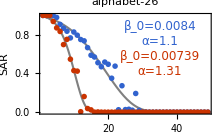

```mathematica
Block[{file,series,models,title},
file=FileNameJoin[{NotebookDirectory[],"letter_replace_13","records","letter_replace_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{t: {m: np.stack([v['L'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(t, {}).items()} for t in d['series'].keys()}"];
models=Association@Flatten[Table[{task,model}->NonlinearModelFit[series[task][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.1},{β,6}},Ν],{task,Keys[series]},{model,Keys[series[task]]}]];
Legended[Column[{Row[Show[Table[Plot[models[{#1,model}][Ν],{Ν,series[#1][model][[1,1]],series[#1][model][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->All,PlotLabel->#2],{model,Keys[series[#1]]}],ListPlot[series[#1],PlotLegends->None],FrameLabel->{"String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{#1,"gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.7,0.8}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{#1,"gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.7,0.5}] ]}]&@@@{{"letter_replace_4","alphabet-4"},{"letter_replace_9","alphabet-9"}}],
Row[Show[Table[Plot[models[{#1,model}][Ν],{Ν,series[#1][model][[1,1]],series[#1][model][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->All,PlotLabel->#2],{model,Keys[series[#1]]}],ListPlot[series[#1],PlotLegends->None],FrameLabel->{"String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{#1,"gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.7,0.8}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{#1,"gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.7,0.5}] ]}]&@@@{{"letter_replace_13","alphabet-13"},{"letter_replace_26","alphabet-26"}}]}],Placed[PointLegend[{Blue,Red},{Style["gemini-2.5-pro",14,FontFamily->"CMU Serif"],Style["gemini-2.5-flash",14,FontFamily->"CMU Serif"]},LegendMarkers->{{"●",10},{"●",10}},LegendLayout->"Row",LabelStyle->{FontSize->10}],Top (*position relative to the graphic—move closer/farther*)]]
]
```

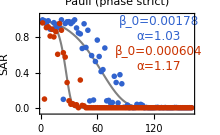
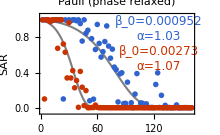

```mathematica
Legended[Row[{Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"direct",model}][Ν],{Ν,series["direct"][model][[1,1]],series["direct"][model][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"Pauli (phase strict)"],{model,Keys[series["direct"]]}],ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.77,0.85}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.77,0.55}] ]}]],
Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"direct",model}][Ν],{Ν,series["direct"][model][[1,1]],series["direct"][model][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"Pauli (phase relaxed)"],{model,Keys[series["direct"]]}],ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.77,0.85}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.77,0.55}] ]}]]}],Placed[PointLegend[{Blue,Red},{Style["gemini-2.5-pro",14,FontFamily->"CMU Serif"],Style["gemini-2.5-flash",14,FontFamily->"CMU Serif"]},LegendMarkers->{{"●",10},{"●",10}},LegendLayout->"Row",LabelStyle->{FontSize->11}],Top ]]
```

{{0.00571371,7.95955,gemini-2.5-pro},{0.0147773,5.46875,gemini-2.5-flash},{0.0181029,5.8958,grok-4-fast-reasoning},{0.00509903,6.88861,claude-sonnet-4-20250514}}

{{0.0434479,10.1013,gpt-5},{0.0786935,4.67379,gemini-2.5-pro},{0.320364,5.30906,gemini-2.5-flash},{0.0429698,6.04058,grok-4-fast-reasoning},{0.163394,5.25297,claude-sonnet-4-20250514}}

{{0.0320904,6.3301,gemini-2.5-pro},{0.155016,7.41114,gemini-2.5-flash}}

{{0.0316575,6.95679,gemini-2.5-pro},{0.066254,5.90217,gemini-2.5-flash}}

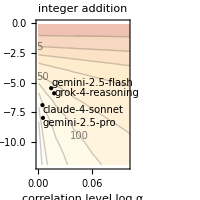
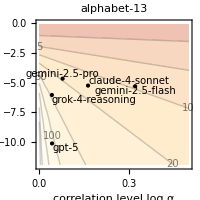
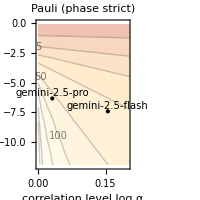
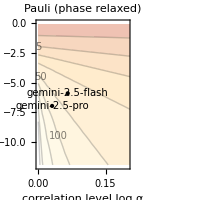

```mathematica
Block[{cfun},
cfun=Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]];
Column[{Row[{Block[{Νcrs},
Print[Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"plus","records","plus_plot.pt"}];
series=GetPy["import torch, numpy as np\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"{k: np.stack([v['L'], v['accuracy']], axis=1).tolist() for k, v in d['series'].items()}"];
models=Association@Table[key->NonlinearModelFit[series[key],Exp[-Ν Exp[α (Ν-1)-β]],{{α,<|"gpt-5"->0.02,"gemini-2.5-flash"->0.01,"gemini-2.5-pro"->0.001,"grok-4-fast-reasoning"->0.1,"claude-sonnet-4-20250514"->0.01|>[key]},{β,<|"gpt-5"->8,"gemini-2.5-flash"->6,"gemini-2.5-pro"->6,"grok-4-fast-reasoning"->6,"claude-sonnet-4-20250514"->6|>[key]}},Ν],{key,Keys@series}];
Table[{α,β,key}/. models[key]["BestFitParameters"],{key,Keys@series}]]];
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.2]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.00571371,7.95955,"gemini-2.5-pro",{-1.2,0.6}},{0.00509903,6.88861,"claude-4-sonnet",{-1.2,0.6}},{0.0181029,5.8958,"grok-4-reasoning",{-1.2,0.2}},{0.0147773,5.46875,"gemini-2.5-flash",{-1.25,-1.}}}}},ColorFunction->cfun,PlotRange->{{0,0.1},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"integer addition",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
Print[Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"letter_replace_13","records","letter_replace_13_plot.pt"}];
series=GetPy["import torch, numpy as np\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"{k: np.stack([v['L'], v['accuracy']], axis=1).tolist() for k, v in d['series'].items()}"];
models=Association@Table[key->NonlinearModelFit[series[key],Exp[-Ν Exp[α (Ν-1)-β]],{{α,<|"gpt-5"->0.02,"gemini-2.5-flash"->0.1,"gemini-2.5-pro"->0.1,"grok-4-fast-reasoning"->0.1,"claude-sonnet-4-20250514"->0.1|>[key]},{β,<|"gpt-5"->8,"gemini-2.5-flash"->6,"gemini-2.5-pro"->6,"grok-4-fast-reasoning"->6,"claude-sonnet-4-20250514"->6|>[key]}},Ν],{key,Keys@series}];
Table[{α,β,key}/. models[key]["BestFitParameters"],{key,Keys@series}]]];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.2]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0434479,10.1013,"gpt-5",{-1.2,0.6}},{0.0786935,4.67379,"gemini-2.5-pro",{-0.4,-1.4}},{0.163394,5.25297,"claude-4-sonnet",{-0.7,-1.1}},{0.0429698,6.04058,"grok-4-reasoning",{-0.7,1.2}},{0.320364,5.30906,"gemini-2.5-flash",{-0.4,1.2}}}}},ColorFunction->cfun,PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"alphabet-13",ImageSize->200]]}],
Row[{
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
Print[Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
{α,β,#1}/. models[{"direct",#1}]["BestFitParameters"]&@@@{{"gemini-2.5-pro"},{"gemini-2.5-flash"}}]];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.2]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0320904,6.3301,"gemini-2.5-pro",{-0.4,-1.3}},{0.155016,7.41114,"gemini-2.5-flash",{0.1,-1.3}}}}},ColorFunction->cfun,PlotRange->{{0,0.2},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"Pauli (phase strict)",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
Print[Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
{α,β,#1}/. models[{"direct",#1}]["BestFitParameters"]&@@@{{"gemini-2.5-pro"},{"gemini-2.5-flash"}}]];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.2]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0316575,6.95679,"gemini-2.5-pro",{-1.2,0}},{0.066254,5.90217,"gemini-2.5-flash",{-1.2,0}}}}},ColorFunction->cfun,PlotRange->{{0,0.2},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"Pauli (phase relaxed)",ImageSize->200]]}]}]]
```

import torch

```mathematica
Print[Block[{file,series,models,title},
file=FileNameJoin[{NotebookDirectory[],"letter_replace_13","records","letter_replace_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{t: {m: np.stack([v['L'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(t, {}).items()} for t in d['series'].keys()}"];
models=Association@Flatten[Table[{task,model}->NonlinearModelFit[series[task][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.1},{β,6}},Ν],{task,Keys[series]},{model,Keys[series[task]]}]];
{α,β,"gemini-2.5-flash"}/. models[{#1,"gemini-2.5-flash"}]["BestFitParameters"]&@@@{{"letter_replace_4","alphabet-4"},{"letter_replace_9","alphabet-9"},{"letter_replace_13","alphabet-13"},{"letter_replace_26","alphabet-26"}}
],
Block[{file,series,models,title},
file=FileNameJoin[{NotebookDirectory[],"letter_replace_13","records","letter_replace_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{t: {m: np.stack([v['L'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(t, {}).items()} for t in d['series'].keys()}"];
models=Association@Flatten[Table[{task,model}->NonlinearModelFit[series[task][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.1},{β,6}},Ν],{task,Keys[series]},{model,Keys[series[task]]}]];
{α,β,"gemini-2.5-pro"}/. models[{#1,"gemini-2.5-pro"}]["BestFitParameters"]&@@@{{"letter_replace_4","alphabet-4"},{"letter_replace_9","alphabet-9"},{"letter_replace_13","alphabet-13"},{"letter_replace_26","alphabet-26"}}
]]
```

{{0.457497,5.11018,gemini-2.5-flash},{0.249114,4.4889,gemini-2.5-flash},{0.320364,5.30906,gemini-2.5-flash},{0.268644,4.90743,gemini-2.5-flash}}{{0.227156,4.81502,gemini-2.5-pro},{0.0755772,4.03505,gemini-2.5-pro},{0.0786935,4.67379,gemini-2.5-pro},{0.0917995,4.77982,gemini-2.5-pro}}

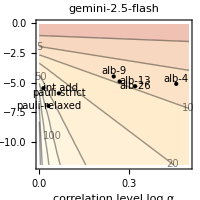
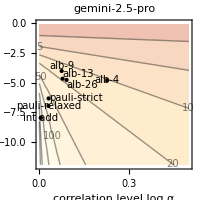
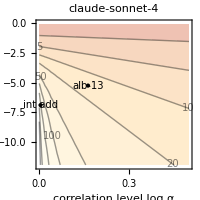
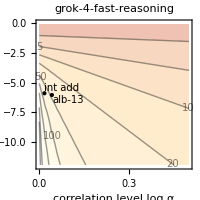
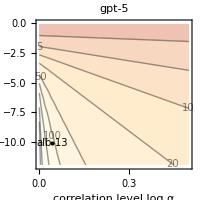

```mathematica
Column[{Row[{Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0147773,5.46875,"int add",{-1.2,-0.4}},{0.457497,5.11018,"alb-4",{-0.,-1.3}},{0.249114,4.4889,"alb-9",{-0.,-1.3}},{0.320364,5.30906,"alb-13",{-0.3,-1.4}},{0.268644,4.90743,"alb-26",{-1.2,1.8}},{0.066254,5.90217,"pauli-strict",{-1.2,0}},{0.0316575,6.95679,"pauli-relaxed",{-1.2,0}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"gemini-2.5-flash",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.00571371,7.95955,"int add",{-1.3,0}},{0.227156,4.81502,"alb-4",{-1.4,0}},{0.0755772,4.03505,"alb-9",{-0.,-1.3}},{0.0786935,4.67379,"alb-13",{-1.3,-0.9}},{0.0917995,4.77982,"alb-26",{-1.2,1.}},{0.0320904,6.3301,"pauli-strict",{-1.2,-0.1}},{0.0316575,6.95679,"pauli-relaxed",{-1.2,0}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"gemini-2.5-pro",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.00509903,6.88861,"int add",{-1.3,0}},{0.163394,5.25297,"alb-13",{-1.4,0}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"claude-sonnet-4",ImageSize->200]]}],
Row[{
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0181029,5.8958,"int add",{-1.1,-1.}},{0.0429698,6.04058,"alb-13",{-1.4,0.6}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"grok-4-fast-reasoning",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0434479,10.1013,"alb-13",{-1.4,0}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"gpt-5",ImageSize->200]]

}]},Alignment->Center]
```

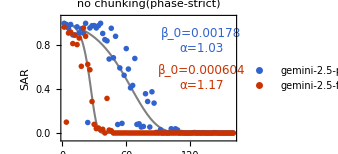
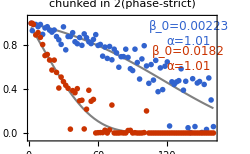
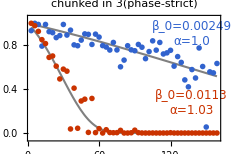
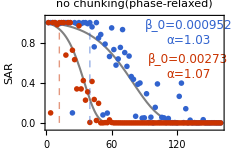
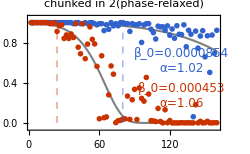
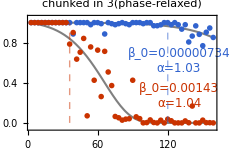

```mathematica
Legended[Column[{Row@{Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"direct",model}][Ν],{Ν,series["direct"][model][[1,1]],series["direct"][model][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"no chunking(phase-strict)"],{model,Keys[series["direct"]]}],ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.8,0.8}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.8,0.5}] ]}]],
Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"k=2",model}][Ν],{Ν,series["k=2"][model][[1,1]],series["k=2"][model][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"chunked in 2(phase-strict)"],{model,Keys[series["k=2"]]}],ListPlot[series["k=2"],PlotLegends->None],FrameLabel->{"",""},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"k=2","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.85,0.85}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"k=2","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.85,0.65}] ]}]
],
Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"k=3",model}][Ν],{Ν,series["k=3"][model][[1,1]],series["k=3"][model][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"chunked in 3(phase-strict)"],{model,Keys[series["k=3"]]}],ListPlot[series["k=3"],PlotLegends->None],FrameLabel->{"",""},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"k=3","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.85,0.85}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"k=3","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.85,0.3}] ]}]
]},
Row@{Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"direct",model}][Ν],{Ν,series["direct"][model][[1,1]],series["direct"][model][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"no chunking(phase-relaxed)"],{model,Keys[series["direct"]]}],ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.8,0.85}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.8,0.55}] ],
{Dashed,Opacity[0.5],Blue,Thick,Line[{{40,0},{40,1}}]},
{Dashed,Opacity[0.5],Red,Thick,Line[{{12,0},{12,1}}]}}]],
Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"k=2",model}][Ν],{Ν,series["k=2"][model][[1,1]],series["k=2"][model][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"chunked in 2(phase-relaxed)"],{model,Keys[series["k=2"]]}],ListPlot[series["k=2"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)",""},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"k=2","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.8,0.6}]],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"k=2","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.8,0.3}]],
{Dashed,Opacity[0.5],Blue,Thick,Line[{{80,0},{80,1}}]},
{Dashed,Opacity[0.5],Red,Thick,Line[{{24,0},{24,1}}]}}]
],
Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"k=3",model}][Ν],{Ν,series["k=3"][model][[1,1]],series["k=3"][model][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"chunked in 3(phase-relaxed)"],{model,Keys[series["k=3"]]}],ListPlot[series["k=3"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)",""},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"k=3","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.8,0.6}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"k=3","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.8,0.3}] ],
{Dashed,Opacity[0.5],Blue,Thick,Line[{{120,0},{120,1}}]},
{Dashed,Opacity[0.5],Red,Thick,Line[{{36,0},{36,1}}]}
}]
]}
},Spacings->{Automatic,-0.8}],Placed[PointLegend[{Blue,Red},{Style["gemini-2.5-pro",14,FontFamily->"CMU Serif"],Style["gemini-2.5-flash",14,FontFamily->"CMU Serif"]},LegendMarkers->{{"●",10},{"●",10}},LegendLayout->"Row",LabelStyle->{FontSize->11}],Top ]]
```

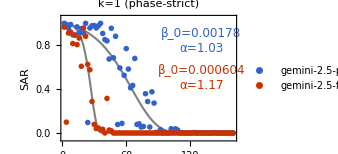
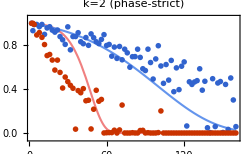
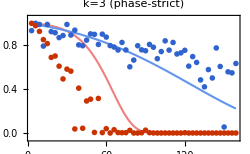
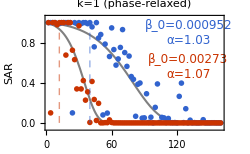
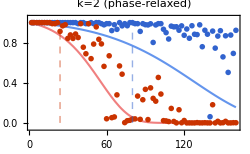
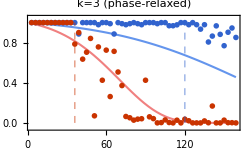

```mathematica
Legended[Column[{Row@{Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"direct",model}][Ν],{Ν,series["direct"][model][[1,1]],series["direct"][model][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k=1 (phase-strict)"],{model,Keys[series["direct"]]}],ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.8,0.8}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.8,0.5}] ]}]],
Block[{file,series,propara,flashpara,k=2},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
propara=Block[{file0,series0,models0},file0=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series0=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file0]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models0=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series0[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series0]},{model,Keys[series0[workflow]]}]];
models0[{"direct","gemini-2.5-pro"}]["BestFitParameters"]];
flashpara=Block[{file0,series0,models0},file0=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series0=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file0]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models0=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series0[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series0]},{model,Keys[series0[workflow]]}]];
models0[{"direct","gemini-2.5-flash"}]["BestFitParameters"]];
Show[Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.flashpara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[-1,1]]},PlotStyle->LightRed,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-strict)"],
Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.propara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[-1,1]]},PlotStyle->LightBlue,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-strict)"]
,ListPlot[series["k="<>ToString[k]<>""],PlotLegends->None],FrameLabel->{"",""}]
],
Block[{file,series,propara,flashpara,k=3},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
propara=Block[{file0,series0,models0},file0=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series0=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file0]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models0=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series0[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series0]},{model,Keys[series0[workflow]]}]];
models0[{"direct","gemini-2.5-pro"}]["BestFitParameters"]];
flashpara=Block[{file0,series0,models0},file0=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series0=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file0]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models0=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series0[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series0]},{model,Keys[series0[workflow]]}]];
models0[{"direct","gemini-2.5-flash"}]["BestFitParameters"]];
Show[Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.flashpara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[-1,1]]},PlotStyle->LightRed,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-strict)"],
Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.propara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[-1,1]]},PlotStyle->LightBlue,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-strict)"]
,ListPlot[series["k="<>ToString[k]<>""],PlotLegends->None],FrameLabel->{"",""}]
]},
Row@{Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
Show[Table[Plot[models[{"direct",model}][Ν],{Ν,series["direct"][model][[1,1]],series["direct"][model][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k=1 (phase-relaxed)"],{model,Keys[series["direct"]]}],ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-pro"}]["BestFitParameters"])),12,Blue,LineSpacing->{0,12}],Scaled[{0.8,0.85}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. models[{"direct","gemini-2.5-flash"}]["BestFitParameters"])),12,Red,LineSpacing->{0,12}],Scaled[{0.8,0.55}] ],
{Dashed,Opacity[0.5],Blue,Thick,Line[{{40,0},{40,1}}]},
{Dashed,Opacity[0.5],Red,Thick,Line[{{12,0},{12,1}}]}}]],
Block[{file,series,propara,flashpara,k=2},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
propara=Block[{file0,series0,models0},file0=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series0=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file0]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models0=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series0[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series0]},{model,Keys[series0[workflow]]}]];
models0[{"direct","gemini-2.5-pro"}]["BestFitParameters"]];
flashpara=Block[{file0,series0,models0},file0=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series0=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file0]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models0=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series0[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series0]},{model,Keys[series0[workflow]]}]];
models0[{"direct","gemini-2.5-flash"}]["BestFitParameters"]];
Show[Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.flashpara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[-1,1]]},PlotStyle->LightRed,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-relaxed)"],
Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.propara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[-1,1]]},PlotStyle->LightBlue,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-relaxed)"]
,ListPlot[series["k="<>ToString[k]<>""],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)",""},
Epilog->{{Dashed,Opacity[0.5],Blue,Thick,Line[{{80,0},{80,1}}]},
{Dashed,Opacity[0.5],Red,Thick,Line[{{24,0},{24,1}}]}
}]
],
Block[{file,series,propara,flashpara,k=3},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
propara=Block[{file0,series0,models0},file0=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series0=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file0]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models0=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series0[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series0]},{model,Keys[series0[workflow]]}]];
models0[{"direct","gemini-2.5-pro"}]["BestFitParameters"]];
flashpara=Block[{file0,series0,models0},file0=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series0=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file0]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models0=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series0[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series0]},{model,Keys[series0[workflow]]}]];
models0[{"direct","gemini-2.5-flash"}]["BestFitParameters"]];
Show[Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.flashpara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[-1,1]]},PlotStyle->LightRed,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-relaxed)"],
Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.propara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[-1,1]]},PlotStyle->LightBlue,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-relaxed)"]
,ListPlot[series["k="<>ToString[k]<>""],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)",""},
Epilog->{{Dashed,Opacity[0.5],Blue,Thick,Line[{{120,0},{120,1}}]},
{Dashed,Opacity[0.5],Red,Thick,Line[{{36,0},{36,1}}]}
}]
]}
},Spacings->{Automatic,-0.8}],Placed[PointLegend[{Blue,Red},{Style["gemini-2.5-pro",14,FontFamily->"CMU Serif"],Style["gemini-2.5-flash",14,FontFamily->"CMU Serif"]},LegendMarkers->{{"●",10},{"●",10}},LegendLayout->"Row",LabelStyle->{FontSize->11}],Top ]]
```

#### Manually tuned

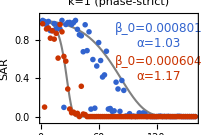
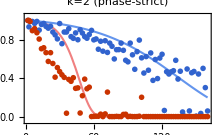
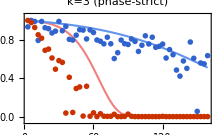
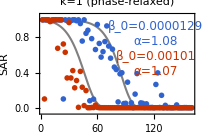
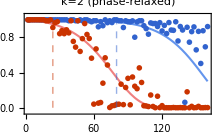
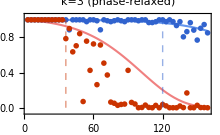

```mathematica
Legended[Column[{Block[{flashpara,propara,g1,g2,g3},
propara={α->0.032090414663624486,β->7.130096749863063};
flashpara={α->0.15501562496418442,β->7.41113856362468};
g1=Block[{file,series},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
Show[Plot[Exp[-Ν Exp[α (Ν-1)-β]]/.flashpara,{Ν,series["direct"]["gemini-2.5-flash"][[1,1]],series["direct"]["gemini-2.5-flash"][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k=1 (phase-strict)"],
Plot[Exp[-Ν Exp[α (Ν-1)-β]]/.propara,{Ν,series["direct"]["gemini-2.5-pro"][[1,1]],series["direct"]["gemini-2.5-pro"][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k=1 (phase-strict)"],
ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. propara)),12,Blue,LineSpacing->{0,12}],Scaled[{0.75,0.8}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. flashpara)),12,Red,LineSpacing->{0,12}],Scaled[{0.75,0.5}] ]}]];
g2=Block[{file,series,k=2},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
Show[Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.flashpara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[-1,1]]},PlotStyle->LightRed,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-strict)"],
Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.propara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[-1,1]]},PlotStyle->LightBlue,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-strict)"]
,ListPlot[series["k="<>ToString[k]<>""],PlotLegends->None],FrameLabel->{"",""}]
];
g3=Block[{file,series,k=3},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
Show[Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.flashpara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[-1,1]]},PlotStyle->LightRed,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-strict)"],
Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.propara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[-1,1]]},PlotStyle->LightBlue,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-strict)"]
,ListPlot[series["k="<>ToString[k]<>""],PlotLegends->None],FrameLabel->{"",""}]
];
Row@{g1,g2,g3}
],
Block[{flashpara,propara,g1,g2,g3},
propara={α->0.08057520132643696,β->11.256792265312429};
flashpara={α->0.06625403176912385,β->6.902173738251426};
g1=Block[{file,series},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
Show[Plot[Exp[-Ν Exp[α (Ν-1)-β]]/.flashpara,{Ν,series["direct"]["gemini-2.5-flash"][[1,1]],series["direct"]["gemini-2.5-flash"][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k=1 (phase-relaxed)"],
Plot[Exp[-Ν Exp[α (Ν-1)-β]]/.propara,{Ν,series["direct"]["gemini-2.5-pro"][[1,1]],series["direct"]["gemini-2.5-pro"][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k=1 (phase-relaxed)"],
ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. propara)),12,Blue,LineSpacing->{0,12}],Scaled[{0.75,0.8}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. flashpara)),12,Red,LineSpacing->{0,12}],Scaled[{0.75,0.5}] ]}]];
g2=Block[{file,series,k=2},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
Show[Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.flashpara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[-1,1]]},PlotStyle->LightRed,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-relaxed)"],
Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.propara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[-1,1]]},PlotStyle->LightBlue,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-relaxed)"]
,ListPlot[series["k="<>ToString[k]<>""],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)",""},
Epilog->{{Dashed,Opacity[0.5],Blue,Thick,Line[{{80,0},{80,1}}]},
{Dashed,Opacity[0.5],Red,Thick,Line[{{24,0},{24,1}}]}
}]
];
g3=Block[{file,series,k=3},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
Show[Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.flashpara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-flash"][[-1,1]]},PlotStyle->LightRed,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-relaxed)"],
Plot[Exp[-Ν Exp[α (Ν/k-1)-β]]/.propara,{Ν,series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[1,1]],series["k="<>ToString[k]<>""]["gemini-2.5-pro"][[-1,1]]},PlotStyle->LightBlue,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k="<>ToString[k]<>" (phase-relaxed)"]
,ListPlot[series["k="<>ToString[k]<>""],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)",""},
Epilog->{{Dashed,Opacity[0.5],Blue,Thick,Line[{{120,0},{120,1}}]},
{Dashed,Opacity[0.5],Red,Thick,Line[{{36,0},{36,1}}]}
}]
];
Row@{g1,g2,g3}
]},Spacings->{Automatic,-0.8}],
Placed[PointLegend[{Blue,Red},{Style["gemini-2.5-pro",14,FontFamily->"CMU Serif"],Style["gemini-2.5-flash",14,FontFamily->"CMU Serif"]},LegendMarkers->{{"●",10},{"●",10}},LegendLayout->"Row",LabelStyle->{FontSize->11}],Top ]]
```

```mathematica
Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
models[{"direct","gemini-2.5-flash"}]["BestFitParameters"]]
```

{α→0.066254,β→5.90217}

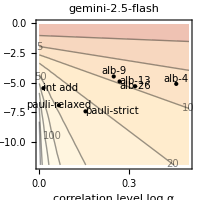
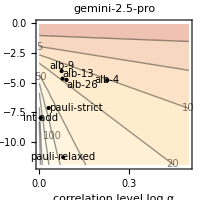
-Graphics--Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Column[{Row[{Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0147773,5.46875,"int add",{-1.2,-0.4}},{0.457497,5.11018,"alb-4",{-0.,-1.3}},{0.249114,4.4889,"alb-9",{-0.,-1.3}},{0.320364,5.30906,"alb-13",{-0.3,-1.4}},{0.268644,4.90743,"alb-26",{-1.2,1.8}},{0.15501562496418442,7.41113856362468,"pauli-strict",{-1.2,0.2}},{0.06625403176912385,6.902173738251426,"pauli-relaxed",{-1.2,0}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"gemini-2.5-flash",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.00571371,7.95955,"int add",{-1.3,0}},{0.227156,4.81502,"alb-4",{-1.4,0}},{0.0755772,4.03505,"alb-9",{-0.,-1.3}},{0.0786935,4.67379,"alb-13",{-1.3,-0.9}},{0.0917995,4.77982,"alb-26",{-1.2,1.}},{0.032090414663624486,7.130096749863063,"pauli-strict",{-1.2,-0.1}},{0.08057520132643696,11.256792265312429,"pauli-relaxed",{-1.2,0}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"gemini-2.5-pro",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.00509903,6.88861,"int add",{-1.3,0}},{0.163394,5.25297,"alb-13",{-1.4,0}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"claude-sonnet-4",ImageSize->200]]}],
Row[{
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0181029,5.8958,"int add",{-1.1,-1.}},{0.0429698,6.04058,"alb-13",{-1.4,0.6}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"grok-4-fast-reasoning",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.4]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0434479,10.1013,"alb-13",{-1.4,0}}}}},ColorFunction->Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]],PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"gpt-5",ImageSize->200]]

}]},Alignment->Center]
```

{{0.00571371,7.95955,gemini-2.5-pro},{0.0147773,5.46875,gemini-2.5-flash},{0.0181029,5.8958,grok-4-fast-reasoning},{0.00509903,6.88861,claude-sonnet-4-20250514}}

{{0.0434479,10.1013,gpt-5},{0.0786935,4.67379,gemini-2.5-pro},{0.320364,5.30906,gemini-2.5-flash},{0.0429698,6.04058,grok-4-fast-reasoning},{0.163394,5.25297,claude-sonnet-4-20250514}}

{{0.0320904,6.3301,gemini-2.5-pro},{0.155016,7.41114,gemini-2.5-flash}}

{{0.0316575,6.95679,gemini-2.5-pro},{0.066254,5.90217,gemini-2.5-flash}}

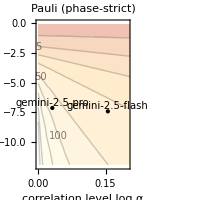
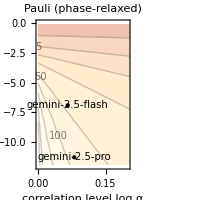
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Block[{cfun},
cfun=Function[{x},Blend[{Lighter[Red,0.7],Lighter[Orange,0.8],Lighter[Yellow,0.9],White},x]];
Column[{Row[{Block[{Νcrs},
Print[Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"plus","records","plus_plot.pt"}];
series=GetPy["import torch, numpy as np\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"{k: np.stack([v['L'], v['accuracy']], axis=1).tolist() for k, v in d['series'].items()}"];
models=Association@Table[key->NonlinearModelFit[series[key],Exp[-Ν Exp[α (Ν-1)-β]],{{α,<|"gpt-5"->0.02,"gemini-2.5-flash"->0.01,"gemini-2.5-pro"->0.001,"grok-4-fast-reasoning"->0.1,"claude-sonnet-4-20250514"->0.01|>[key]},{β,<|"gpt-5"->8,"gemini-2.5-flash"->6,"gemini-2.5-pro"->6,"grok-4-fast-reasoning"->6,"claude-sonnet-4-20250514"->6|>[key]}},Ν],{key,Keys@series}];
Table[{α,β,key}/. models[key]["BestFitParameters"],{key,Keys@series}]]];
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.2]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.00571371,7.95955,"gemini-2.5-pro",{-1.2,0.6}},{0.00509903,6.88861,"claude-4-sonnet",{-1.2,0.6}},{0.0181029,5.8958,"grok-4-reasoning",{-1.2,0.2}},{0.0147773,5.46875,"gemini-2.5-flash",{-1.25,-1.}}}}},ColorFunction->cfun,PlotRange->{{0,0.1},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"integer addition",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
Print[Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"letter_replace_13","records","letter_replace_13_plot.pt"}];
series=GetPy["import torch, numpy as np\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"{k: np.stack([v['L'], v['accuracy']], axis=1).tolist() for k, v in d['series'].items()}"];
models=Association@Table[key->NonlinearModelFit[series[key],Exp[-Ν Exp[α (Ν-1)-β]],{{α,<|"gpt-5"->0.02,"gemini-2.5-flash"->0.1,"gemini-2.5-pro"->0.1,"grok-4-fast-reasoning"->0.1,"claude-sonnet-4-20250514"->0.1|>[key]},{β,<|"gpt-5"->8,"gemini-2.5-flash"->6,"gemini-2.5-pro"->6,"grok-4-fast-reasoning"->6,"claude-sonnet-4-20250514"->6|>[key]}},Ν],{key,Keys@series}];
Table[{α,β,key}/. models[key]["BestFitParameters"],{key,Keys@series}]]];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.2]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.0434479,10.1013,"gpt-5",{-1.2,0.6}},{0.0786935,4.67379,"gemini-2.5-pro",{-0.4,-1.4}},{0.163394,5.25297,"claude-4-sonnet",{-0.7,-1.1}},{0.0429698,6.04058,"grok-4-reasoning",{-0.7,1.2}},{0.320364,5.30906,"gemini-2.5-flash",{-0.4,1.2}}}}},ColorFunction->cfun,PlotRange->{{0,0.5},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"alphabet-13",ImageSize->200]]}],
Row[{
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
Print[Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
{α,β,#1}/. models[{"direct",#1}]["BestFitParameters"]&@@@{{"gemini-2.5-pro"},{"gemini-2.5-flash"}}]];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.2]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.032090414663624486,7.130096749863063,"gemini-2.5-pro",{-0.4,-1.3}},{0.15501562496418442,7.41113856362468,"gemini-2.5-flash",{0.1,-1.3}}}}},ColorFunction->cfun,PlotRange->{{0,0.2},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"Pauli (phase-strict)",ImageSize->200]],
Block[{Νcrs},
Νcrs[α_?NumericQ,β_?NumericQ]:=Exp[logΝ]/.FindRoot[-Exp[logΝ] Exp[α (Exp[logΝ]-1)-β]==Log[1/2],{logΝ,Log[β/α]}];
Print[Block[{file,series,models},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
models=Association@Flatten[Table[{workflow,model}->NonlinearModelFit[series[workflow][model],Exp[-Ν Exp[α (Ν-1)-β]],{{α,0.01},{β,6}},Ν],{workflow,Keys[series]},{model,Keys[series[workflow]]}]];
{α,β,#1}/. models[{"direct",#1}]["BestFitParameters"]&@@@{{"gemini-2.5-pro"},{"gemini-2.5-flash"}}]];
ListContourPlot[Flatten[Table[{α,-β,Log[10,Νcrs[α,β]]},{α,Join[Range[0.001,0.01,0.001],Range[0.02,0.5,0.02]]},{β,0.1,12,0.2}],1],Contours->Log[10,{2,5,10,20,50,100,200,500,1000}],ContourLabels->Function[{x,y,z},If[MemberQ[{100,50,20,10,5},10^z],Text[Style[ToString[10^z],10,Opacity[0.5]],{x,y}],Nothing]],ContourStyle->Directive[AbsoluteThickness[1],Opacity[0.2]],Epilog->{{Translate[{Point[{0,0}],Text[Style[#3,10],{0,0},#4]},{#1,-#2}]&@@@{{0.08057520132643696,11.256792265312429,"gemini-2.5-pro",{-1.2,0}},{0.06625403176912385,6.902173738251426,"gemini-2.5-flash",{-1.2,0}}}}},ColorFunction->cfun,PlotRange->{{0,0.2},{-12,0},All},FrameLabel->{"correlation level \!\(log α\)","error level \!\(log β\_0\)"},PlotLabel->"Pauli (phase-relaxed)",ImageSize->200]]}]}]]
```

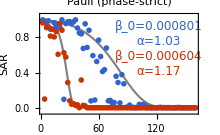
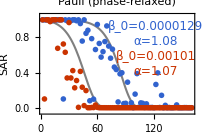

```mathematica
Legended[Row[{Block[{file,series,flashpara,propara},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['accuracy']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
propara={α->0.032090414663624486,β->7.130096749863063};
flashpara={α->0.15501562496418442,β->7.41113856362468};
Show[Plot[Exp[-Ν Exp[α (Ν-1)-β]]/.flashpara,{Ν,series["direct"]["gemini-2.5-flash"][[1,1]],series["direct"]["gemini-2.5-flash"][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"Pauli (phase-strict)"],
Plot[Exp[-Ν Exp[α (Ν-1)-β]]/.propara,{Ν,series["direct"]["gemini-2.5-pro"][[1,1]],series["direct"]["gemini-2.5-pro"][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k=1 (phase-strict)"],
ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. propara)),12,Blue,LineSpacing->{0,12}],Scaled[{0.75,0.8}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. flashpara)),12,Red,LineSpacing->{0,12}],Scaled[{0.75,0.5}] ]}]],
Block[{file,series,flashpara,propara},file=FileNameJoin[{NotebookDirectory[],"direct_multiplication","records","pauli_multiply_all_plot.pt"}];
series=GetPy["import torch\n"<>"d = torch.load(r'''"<>ToString[file]<>"''')\n"<>"import numpy as np\n"<>"{w: {m: np.stack([v['N'], v['acc_string']], axis=1).tolist() for (m, v) in d['series'].get(w, {}).items()} for w in d['series'].keys()}"];
propara={α->0.08057520132643696,β->11.256792265312429};
flashpara={α->0.06625403176912385,β->6.902173738251426};
Show[Plot[Exp[-Ν Exp[α (Ν-1)-β]]/.flashpara,{Ν,series["direct"]["gemini-2.5-flash"][[1,1]],series["direct"]["gemini-2.5-flash"][[-1,1]]},PlotStyle->Gray,ImageSize->220,PlotRange->{All,{-0.05,1.05}},PlotLabel->"Pauli (phase-relaxed)"],
Plot[Exp[-Ν Exp[α (Ν-1)-β]]/.propara,{Ν,series["direct"]["gemini-2.5-pro"][[1,1]],series["direct"]["gemini-2.5-pro"][[-1,1]]},PlotStyle->Gray,ImageSize->250,PlotRange->{All,{-0.05,1.05}},PlotLabel->"k=1 (phase-relaxed)"],
ListPlot[series["direct"],PlotLegends->None],FrameLabel->{"Pauli String length \!\(N\)","SAR"},
Epilog->{Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. propara)),12,Blue,LineSpacing->{0,12}],Scaled[{0.75,0.8}] ],Text[Style[StringTemplate["\!\(β\_0=`1`\)\n\!\(α=`2`\)"]@@(NumberForm[#,3]&/@({Exp[-β],Exp[α]}/. flashpara)),12,Red,LineSpacing->{0,12}],Scaled[{0.75,0.5}] ]}]]}],Placed[PointLegend[{Blue,Red},{Style["gemini-2.5-pro",14,FontFamily->"CMU Serif"],Style["gemini-2.5-flash",14,FontFamily->"CMU Serif"]},LegendMarkers->{{"●",10},{"●",10}},LegendLayout->"Row",LabelStyle->{FontSize->11}],Top ]]
```